```mathematica
f[x_,a_:a,b_:b,c_:c]=Collect[Expand[(x-a)(x-b)(x-c)],x]
third[a_,b_]=Solve[f'[1]==1,{c}][[1,1,2]]
aa=2/16
bb=8/16
cc=third[aa,bb]
f[x,aa,bb,cc]
f'[x,aa,bb,cc]
Plot[f[x,aa,bb,cc],{x,0,1}]
```

-Sin[6 π x]/(36 π^2)

Sin[6 π x]

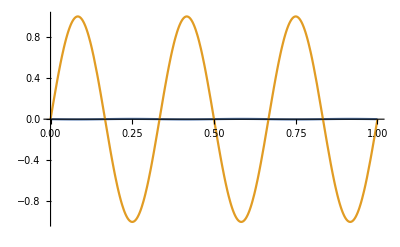

```mathematica
f[x_]:=Sin[x 6π]/(-(6π)^2)
f[x]
f''[x]
Plot[{f[x],f''[x]},{x,0,1}]
```